# 2D pot Well

```mathematica
V[Gx_,Gy_]:=Integrate[V0/Vcell*Exp[ⅈ*(Gx*x+Gy*y)],{x,xL,xR},{y,yL,yR}];
V[0,0]
V[0,ΔGy]
V[ΔGx,0]
V[ΔGx,ΔGy]
Numerator[V[0,ΔGy]];
Numerator[V[ΔGx,0]];
Numerator[V[ΔGx,ΔGy]];
```

(V0 (-xL+xR) (-yL+yR))/Vcell

(ⅈ (ⅇ^(ⅈ yL ΔGy)-ⅇ^(ⅈ yR ΔGy)) V0 (-xL+xR))/(Vcell ΔGy)

-(ⅈ (ⅇ^(ⅈ xL ΔGx)-ⅇ^(ⅈ xR ΔGx)) V0 (yL-yR))/(Vcell ΔGx)

-((ⅇ^(ⅈ xL ΔGx)-ⅇ^(ⅈ xR ΔGx)) (ⅇ^(ⅈ yL ΔGy)-ⅇ^(ⅈ yR ΔGy)) V0)/(Vcell ΔGx ΔGy)

# Descending Well

## descending potential

```mathematica
xL = -3.0;
xR = 4.1;
V0 = -1.0;
ΔV= 1.0;
V[x_,y_]:=V0 - ΔV*(x-xL)/(xR-xL);

Plot[V[x,1],{x,xL,xR}]
```

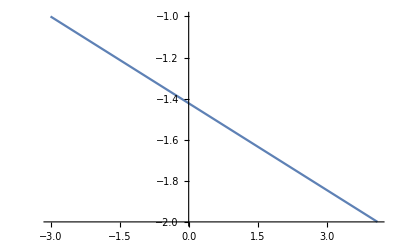

## Integrate descending pot

```mathematica
Clear[xL,xR,V0,ΔV];
ΔV=ΔV
V[x_,y_]:=V0 - ΔV*(x-xL)/(xR-xL);
Vint[Gx_,Gy_]:=Integrate[V[x,y]*Exp[ⅈ*(Gx*x+Gy*y)]/vol,{x,xL,xR},{y,yL,yR}];
Vint[0,0]
Vint[0,Gy]
Vint[Gx,0]
Vint[Gx,Gy]
Integrate[x*Exp[ⅈ*Gx*x],{x,xL,xR}];
```

ΔV

((xL-xR) (yL-yR) (2 V0-ΔV))/(2 vol)

-(ⅈ (ⅇ^(ⅈ Gy yL)-ⅇ^(ⅈ Gy yR)) (xL-xR) (2 V0-ΔV))/(2 Gy vol)

1/(Gx^2 vol (xL-xR))ⅈ (-yL+yR) (ⅇ^(ⅈ Gx xL) (Gx V0 (xL-xR)+ⅈ ΔV)-ⅇ^(ⅈ Gx xR) (Gx (xL-xR) (V0-ΔV)+ⅈ ΔV))

-(((ⅇ^(ⅈ Gy yL)-ⅇ^(ⅈ Gy yR)) (ⅇ^(ⅈ Gx xL) (Gx V0 (xL-xR)+ⅈ ΔV)-ⅇ^(ⅈ Gx xR) (Gx (xL-xR) (V0-ΔV)+ⅈ ΔV)))/(Gx^2 Gy vol (xL-xR)))